{{wx→(√(15/13))/2,wy→-11/(2 √65)},{wx→-(√(15/13))/2,wy→11/(2 √65)}}

1.61245

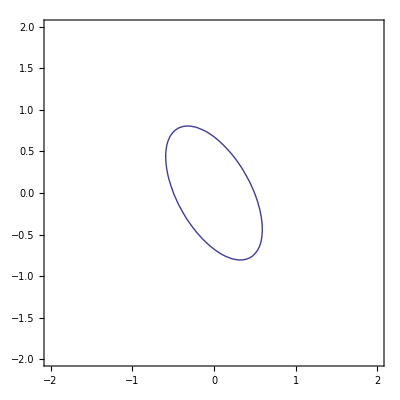

{{1,1/4},{{√3,1},{-1/(√3),1}}}

```mathematica
ClearAll["Global`*"]
$T = 1/10;
$D = {{13/16, 3√3/16},{3√3/16, 7/16}};
MatrixForm[%];
zT1 := {x,y}.$D.{x,y}/2;
v1 = {√3/2, 1/2};
v2 = {1/2, √3/2};
$v = v2;
$w := {wx,wy};
$sol = Solve[{$w.$D.$w/2 == $T, $v.$D.$w  ==0},$w]
$w = $w/.$sol[[2]];

width = N[2*{-$v[[2]], $v[[1]]}.$w]

Show[ContourPlot[{zT1==$T}, {x,-2,2}, {y, -2,2}]]

Eigensystem[$D]
$vec = {√3,1};
$Left = $w.$D.$w;
$Right =
```